```mathematica
data:={{29.2,3040},{30.7,3840},{24.7,2470},{32.3,3610},{31.3,3480},{31.5,3810},{24.5,2330},{19.9,1800},{27.3,3110},{27.1,3160},{24.0,2310},{33.8,4360},{21.5,1880},{32.2,3670},{22.5,1740},{27.5,2250},{25.6,2650},{34.5,4970},{26.2,2620},{26.7,2900},{21.1,1671},{24.1,2540},{32.7,3800},{32.6,4600},{22.1,1900},{25.3,2530},{30.8,2920},{38.9,4990},{22.1,1670},{29.2,3310},{30.1,3450},{31.4,3600},{26.7,2850},{22.1,1590},{30.3,3770},{32.0,3850},{23.2,2480},{30.3,3570},{29.9,2620},{20.8,1890},{33.2,3030},{28.2,3030}}
```

```mathematica
model=LinearModelFit[data, x, x]
```

FittedModel[-2149.4+184.545 x]

```mathematica
residuals=model["FitResiduals"]
```

{-199.306,323.877,61.1446,-201.395,-146.85,146.241,-41.9464,276.959,221.329,308.237,30.3259,271.788,61.6875,-122.94,-262.857,-675.58,75.0545,752.607,-65.6723,122.055,-73.4946,241.871,-85.2125,733.242,-29.0393,10.4178,-614.578,-39.3894,-259.039,70.6937,44.6035,-45.3045,72.0553,-339.039,327.695,93.9687,347.962,127.695,-748.488,200.869,-947.485,-24.7616}

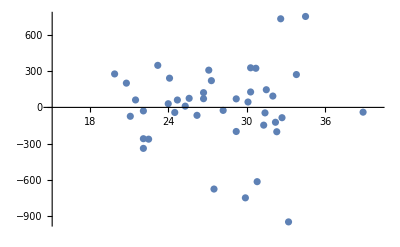

```mathematica
ListPlot[Table[{data[[i]][[1]], residuals[[i]]}, {i,1,42}],PlotRange->{{15,40},Automatic}]
```